# Composite Operators in Yukawa Theory

Derive correlation functions of the fermion bilinear O = Psibar Psi in Yukawa theory using that  <F(phi)> = F[Phi + Propagator . d/dPhi].
We compute here <O> and <O(p) O(q)>.

## Setup

```mathematica
Get["FunKit`"]
```

Mathematica package TensorBases loaded

Authors: Andreas Geißel, Franz Richard Sattler

Version: 1.0

Year: 2025

For a list of available bases, call TBInfo[]. For further information on a particular basis, call TBInfo["BasisName"].

This package provides the methods TBGetBasisElement, TBGetInnerProduct, TBGetMetric, TBGetInverseMetric, TBGetProjector for every tensor basis available.

For closer explanations, please call their usage messages, e.g. TBGetProjector::usage.

Other useful tools include TBBasisTransformation, TBVertexTransformation, TBGetIdentityMatrix, TBGetBasisSize, TBGetIndexSet, TBMakePropagator.

To build or manipulate bases, please call TBInfo["BaseBuilder"].

To show information on the used notation, call TBInfo["Notation"].

FormTracer package loaded.

To see all (user-defined and package-defined) FormTracer definitions, call TBInfo["FormTracer"].

Furthermore, TensorBases extends FormTracer. To see all extensions, call TBInfo["Extensions"]

To see all momentum transformations that can be performed by TensorBases, call TBInfo["Momenta"].

Lorentz group undefined, using default names.

Group with name color undefined, using default names.

Group with name flavor undefined, using default names.

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 0.4.0
Year: 2025
For more information and a brief introduction to the package, call FInfo[].
To run the testing suite, you can call  FTest[].

Yukawa fields: real scalar Phi, Dirac fermion (Psibar, Psi). Truncation includes the Yukawa vertex and the four-fermion vertex.

```mathematica
fields = <|
"Commuting"->{Phi[p]},
"Grassmann"->{{Psibar[p,{a}],Psi[p,{a}]}}
|>;

truncation = <|
Rdot->{{Phi,Phi},{Psi,Psibar}},
Propagator -> {{Phi, Phi}, {Psi, Psibar}},
GammaN     -> {{Phi}, {Psi, Psibar}, {Phi, Phi},{Psi, Psibar, Phi},{Psibar, Psibar, Psi, Psi}},
Field->{{}}
|>;

setup = <|"FieldSpace"->fields,"Truncation"->truncation|>;
FSetGlobalSetup[setup];
FSetTexStyles[Psi->"\\psi",Psibar->"\\bar{\\psi}",Phi->"\\phi"];
```

## Composite operator and replacement rule

The composite operator O(idx) = Psibar(idx) Psi(idx). Both fermions share one super-index, which contracts their internal indices.

```mathematica
COp[idx_] := FEx[FTerm[Psibar[Symbol[SymbolName[idx]<>"1"]], Psi[Symbol[SymbolName[idx]<>"2"]]]];
```

phiToPhiPlusGD substitutes phi -> Phi + G*δ/δPhi for every elementary field. For that we first create the corresponding replacements list:

```mathematica
allFields = {Phi, Psibar, Psi};
insertDerivatives=Map[(#[id_] :> Module[{i},
FEx[FTerm[#[id]],FTerm[Propagator[{#,AnyField},{id,i}],FDOp[AnyField[i]]]]
])&,
allFields
]
```

{Phi[id_]:>Module[{i},FEx[FTerm[Phi[id]],FTerm[Propagator[{Phi,AnyField},{id,i}],FDOp[AnyField[i]]]]],Psibar[id_]:>Module[{i},FEx[FTerm[Psibar[id]],FTerm[Propagator[{Psibar,AnyField},{id,i}],FDOp[AnyField[i]]]]],Psi[id_]:>Module[{i},FEx[FTerm[Psi[id]],FTerm[Propagator[{Psi,AnyField},{id,i}],FDOp[AnyField[i]]]]]}

And then, for convenience, the actual function to insert the substitutions:

```mathematica
phiToPhiPlusGD[expr_]:=Replace[expr,insertDerivatives,{2}];
```

## One-point <O>

Apply the rule to the single FTerm of O(i1), resolve, truncate. The surviving diagram is the chiral condensate.

```mathematica
oneOpRaw=COp[i];
oneOpExpanded=oneOpRaw//phiToPhiPlusGD;
Gop1Pt=oneOpExpanded//FResolveDerivatives//FTruncate;
Gop1Pt//FPrint//FPlot;
```

-Graphics-

-Graphics--Graphics-

## Two-point <O(p) O(q)>

Build the operator product, apply the rule to all four fields (giving 2^4 = 16 terms), resolve, set sources to zero, truncate.

-Graphics-+-Graphics-+-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

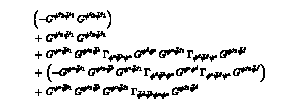

```mathematica
twoOpRaw=COp[i]**COp[j];
twoOpExpanded=twoOpRaw//phiToPhiPlusGD;
Gop2Pt=twoOpExpanded//FResolveDerivatives//FTruncate;
Gop2Pt//FPlot//FPrint;
```